## K-states representation for the wave functions |IMK>

```mathematica
ClearAll["Global`*"]
```

## Constants

```mathematica
angles={π/3,π/5,π/7};
spin=3;
```

## Wigner functions

```mathematica
wd[spin_,m_,k_,angles_]:=WignerD[{spin,m,k},angles[[1]],angles[[2]],angles[[3]]];
wdreal[spin_,m_,k_,angles_]:=Re[wd[spin,m,k,angles]];
```

```mathematica
Kstates[spin_,k_,angles_]:=Table[N[wdreal[spin,mi,k,angles]],{mi,-spin,spin,1}];
```

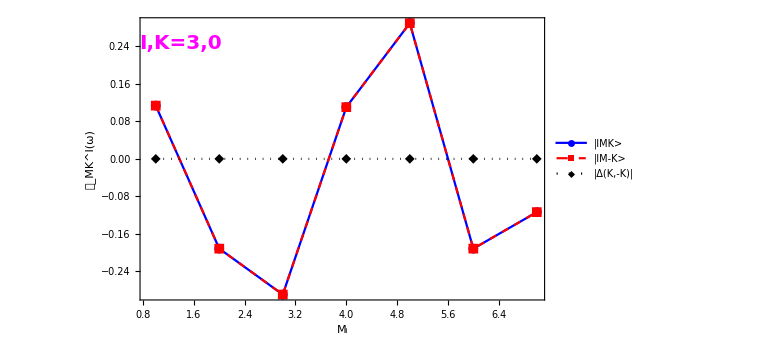
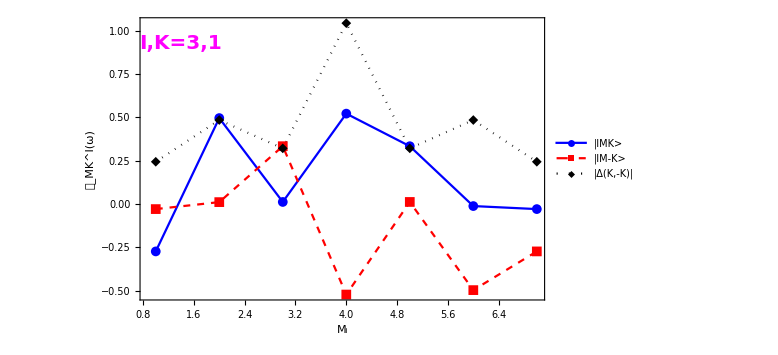
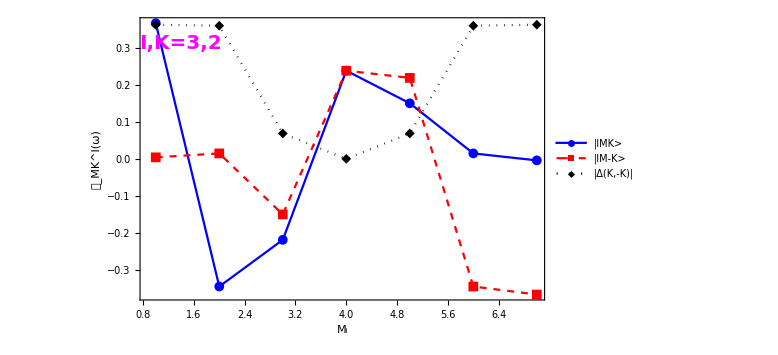
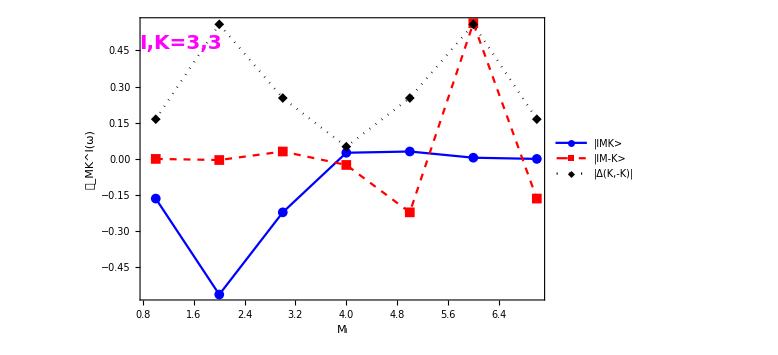
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
pairplot[spin_,k_,angles_]:=ListPlot[{Kstates[spin,-k,angles],Kstates[spin,k,angles],Abs[Kstates[spin,-k,angles]-Kstates[spin,k,angles]]},Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,PlotRange->All,PlotStyle->{{Blue},{Red,Dashed},{Black,Dotted}},FrameStyle->Directive[Black,Thick],FrameLabel->{"M_i","𝒟_MK^I(ω)"},LabelStyle->{18,Black,Bold,FontFamily->"Times"},ImageSize->Large,PlotLegends->{"|IMK>","|IM-K>","|Δ(K,-K)|"},Epilog->Inset[Style[StringTemplate["I,K=``,``"][spin,k],20,Bold,Magenta,Italic],Scaled[{0.1,0.91}]]];
Grid[{{pairplot[3,0,angles],pairplot[3,1,angles]},{pairplot[3,2,angles],pairplot[3,3,angles]}}]
```

### Create a list plot with all the K values in a tabular form (with M running over the possible values)

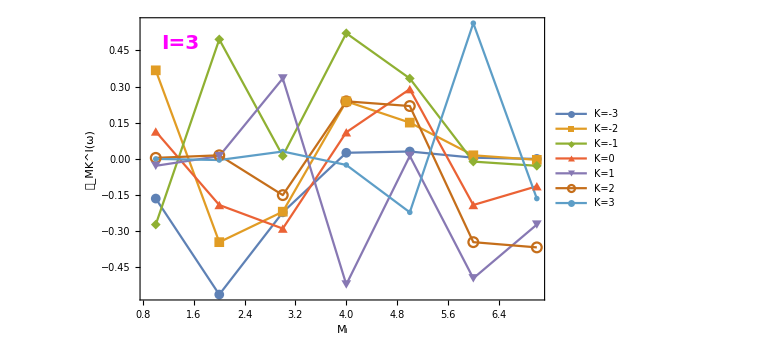

```mathematica
makelegends[spin_]:=Table[Style[StringTemplate["K=``"][-spin+(i-1)]],{i,1,2*spin+1}];
dataPlot[spin_,angles_]:=ListPlot[Table[Kstates[spin,ki,angles],{ki,-spin,spin,1}],Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,PlotRange->All,FrameStyle->Directive[Black,Thick],FrameLabel->{"M_i","𝒟_MK^I(ω)"},LabelStyle->{18,Black,Bold,FontFamily->"Times"},ImageSize->Large,Epilog->Inset[Style[StringTemplate["I=``"][spin],20,Bold,Magenta,Italic],Scaled[{0.1,0.91}]],PlotLegends->Placed[makelegends[spin],Right]];
dataPlot[3,angles]
```

## Calculate the squared sum for the Wigner-D functions

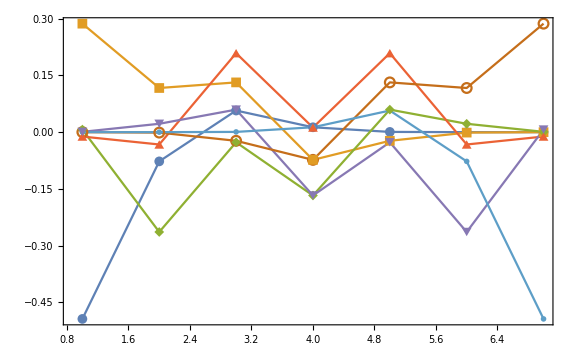

```mathematica
wdSum[spin_,angles_]:=Table[wd[spin,p,q,angles],{p,-spin,spin,+1},{q,-spin,spin,1}];
sumtable=wdSum[spin,angles]^2;
ListPlot[N[Re[sumtable]],Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,PlotRange->Full,ImageSize->Large]
```

## Optimize the Wigner D functions

```mathematica
wdplotter[spin_,angles_]:=ListPlot[{Table[Kstates[spin,k,angles],{k,-spin,spin,1}],Table[Mstates[spin,m,angles],{m,-spin,spin,1}]},Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,PlotRange->Full];
wdplotter[spin,angles]
```

ListPlot::lpn: {{},{{1.,Mstates[3.,-3.,{1.0472,0.628319,0.448799}]},{2.,Mstates[3.,-2.,{1.0472,0.628319,0.448799}]},{3.,Mstates[3.,-1.,{1.0472,0.628319,0.448799}]},{4.,Mstates[3.,0.,{1.0472,0.628319,0.448799}]},{5.,Mstates[3.,1.,{1.0472,0.628319,0.448799}]},{6.,Mstates[3.,2.,{1.0472,0.628319,0.448799}]},{7.,Mstates[3.,3.,{1.0472,0.628319,0.448799}]}}} is not a list of numbers or pairs of numbers.

ListPlot[{{{-0.164668,-0.562799,-0.221805,0.0252611,0.0305247,0.00481203,-0.00019376},{0.367214,-0.345483,-0.219134,0.23863,0.150372,0.0147483,-0.00409282},{-0.272612,0.495583,0.0122929,0.521124,0.333501,-0.0113642,-0.0287804},{0.113522,-0.191366,-0.289202,0.110246,0.289202,-0.191366,-0.113522},{-0.0287804,0.0113642,0.333501,-0.521124,0.0122929,-0.495583,-0.272612},{0.00409282,0.0147483,-0.150372,0.23863,0.219134,-0.345483,-0.367214},{-0.00019376,-0.00481203,0.0305247,-0.0252611,-0.221805,0.562799,-0.164668}},{Mstates[3,-3,{π/3,π/5,π/7}],Mstates[3,-2,{π/3,π/5,π/7}],Mstates[3,-1,{π/3,π/5,π/7}],Mstates[3,0,{π/3,π/5,π/7}],Mstates[3,1,{π/3,π/5,π/7}],Mstates[3,2,{π/3,π/5,π/7}],Mstates[3,3,{π/3,π/5,π/7}]}},Joined→True,PlotMarkers→{Automatic,Medium},Frame→True,PlotRange→Full]